# Neutrino Propagation in Supernovae with Non-Standard Interactions (beyond the Standard Model of Elementary Particles)

A lesson on how Wolfram Language can be used to create a simple toy model 
that can efficiently guide towards understanding general features of complex systems

## Setting up a system of interacting neutrinos and antineutrinos with two distinct types (electron neutrino/antineutrino or non-electron neutrino/antineutrino)

COMMENT: 
In case you would like to learn more about the system, please, see: https://journals.aps.org/prd/abstract/10.1103/PhysRevD.94.093007

First we define a toy function to describe the shape of the background potential caused by neutrinos interacting with other non-neutrino background particles
(including non-standard interaction contributions which are assumed to behave similarly as weak interactions):

```mathematica
potBG[yshiftBG_,xshiftBG_,widthBG_,r_]:=(yshiftBG-((r-xshiftBG)/widthBG)^2 );
(* 
yshiftBG can be used to adjust a shift along y-axis,
xshiftBG can be used to adjust a shift along x-axis, 
widthBG canb be used to adjust width of the potential,
r describes the radial distance from the emission location
*)
```

Next we define a function to describe the shape of the background potential caused by neutrinos interacting with other surrounding neutrinos and antineutrinos:

```mathematica
potNu[scaleNu_,steepnessNu_,r_]:=scaleNu Exp[-r/steepnessNu];
potAnu[asymmetry_,scaleNu_,steepnessNu_,r_]:=-asymmetry potNu[scaleNu,steepnessNu,r];
(*
potNu[scaleNu_,steepnessNu_,r_] describes the neutrino potential, 
scaleNu can be used to adjust intial scaling of the potential,
steepnessNu can be used to adjust steepness of the potential,
potAnu[asymmetry_,scaleNu_,steepnessNu_,r_] describes the antineutrino potential (which is assumed to scale linearly with respect to the neutrino potential),
asymmetry describes the initial asymmetry between neutrinos and antineutrinos,
r describes the radial distance from the emission location
*)
```

Now we can visualize the different possible extreme configurations for the potentials with some interesting input values:

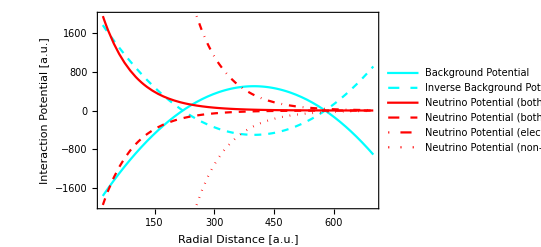

```mathematica
yBG=400 (* an example value for yshiftBG *);
xBG=500 (* an example value for xshiftBG *);
wBG=8 (* an example value for widthBG *);

scNu=25000 (* an example value for scaleNu *);
stNu=80 (* an example value for steepnessNu *);
as=0.9 (* an example value for the initial neutrino-antineutrino asymmetry *);

rmin=20  (* initial radial evaluation point *); 
rmax=700 (* final radial evaluation point *); 

Plot[{
potBG[xBG,yBG,wBG,r] (* background potential *),
-potBG[xBG,yBG,wBG,r] (* inverse of the background potential *),
potNu[scNu,stNu,r]+potAnu[as,scNu,stNu,r] (* total neutrino potential, with electron type neutrinos and antineutrinos *),
-potNu[scNu,stNu,r]-potAnu[as,scNu,stNu,r]  (* total neutrino potential, with non-electron type neutrinos and antineutrinos *),
potNu[scNu,stNu,r]-potAnu[as,scNu,stNu,r] (* total neutrino potential with electron type neutrinos and non-electron type antineutrinos *), 
-potNu[scNu,stNu,r]+potAnu[as,scNu,stNu,r] } (* total neutrino potential with non-electron type neutrinos and electron type antineutrinos *),
{r,rmin,rmax},Frame->True,
PlotStyle->{Cyan,{Cyan,Dashed},Red,{Red,Dashed},{Red,DotDashed},{Red,Dotted}},
FrameLabel->{"Radial Distance [a.u.]","Interaction Potential [a.u.]"},
FrameTicksStyle->Thick,
LabelStyle->Directive[FontSize->20],PlotLegends->{"Background Potential","Inverse Background Potential","Neutrino Potential (both electron type)","Neutrino Potential (both non-electron type)","Neutrino Potential (electron neutrino, non-electron antineutrino)","Neutrino Potential (non-electron neutrino, electron antineutrino)"}
]
```

## Simulating the evolution of neutrinos and antineutrinos

In this section we will set up the equations that allow us to follow the evolution of neutrinos and antineutrinos using density matrix formalism.

First, we need to define Hamiltonian describing non-interacting neutrinos:

```mathematica
mix=0.15 (* a quantity describing internal quantum mixing between the different neutrino types *);
Hv=0.5 {{-Cos[2 mix],Sin[2 mix]},{Sin[2 mix],Cos[2 mix]}} (* Hamiltonian describing two types of non-interacting mixed neutrinos *);
```

Next, we define the Hamiltonian describing the “non-neutrino” background contributions as described in the previous section:

```mathematica
Hbg=potBG[xBG,yBG,wBG,r] DiagonalMatrix[{1,0}] (* notice the coupling only to electron component! *);
```

Finally, we define the Hamiltonian describing the neutrino interactions with other neutrinos and antineutrinos using neutrino and antineutrino density matrices:

```mathematica
rho = {{r11[r],r12[r]},{r21[r],r22[r]}} (* explicitly defined neutrino density matrix with unknown components *);
rhob = {{rb11[r],rb12[r]},{rb21[r],rb22[r]}} (* explicitly defined antineutrino density matrix with unknown components *);
Hnu=potNu[scNu,stNu,r] (rho-as Conjugate[rhob]) (* total Hamiltonian due to neutrino interactions with other neutrinos and antineutrinos *);
```

The total Hamiltonians for neutrinos and antineutrinos depend on all of the above contributions:

```mathematica
Htotnu=Hv+Hbg+Hnu (* total neutrino Hamiltonian *);
Htotanu=Hv-Hbg-Conjugate[Hnu](* total antineutrino Hamiltonian *);
```

We are ready to set up the evolution equations for the density matrices using Liouville-von Neumann equations
(notice that the evolution equations are non-linear!):

```mathematica
rdot=-I (Htotnu.rho-rho.Htotnu) (* right-hand-side of the Liouville-von Neumann equation for neutrinos *);
rbdot=-I (Htotanu.rhob-rhob.Htotanu)(* right-hand-side of the Liouville-von Neumann equation for antineutrinos *);
```

Now we can use NDSolve to solve the evolution equations (notice that the evolution equations for neutrinos and antineutrinos are coupled!):

```mathematica
solevo=NDSolve[
{(* neutrino and antineutrino evolution equations written explictly for all components: *)
r11'[r]==rdot[[1,1]],
r12'[r]==rdot[[1,2]],
r21'[r]==rdot[[2,1]],
r22'[r]==rdot[[2,2]],
rb11'[r]==rbdot[[1,1]],
rb12'[r]==rbdot[[1,2]],
rb21'[r]==rbdot[[2,1]],
rb22'[r]==rbdot[[2,2]],
r11[rmin]==1,r12[rmin]== 0,r21[rmin]==0,r22[rmin]==0  (* initial conditions for neutrinos assuming electron type neutrinos *),
rb11[rmin]==1,rb12[rmin]== 0,rb21[rmin]==0,rb22[rmin]==0 (* initial conditions for antineutrinos assuming electron type antineutrinos *)
},
{r11,r12,r21,r22,rb11,rb12,rb21,rb22} (* list of unknown variables for NDSolve *),
{r,rmin,rmax} (* range of integration (over the radial coordinate) *)
,MaxSteps->10000000];

nu11[r_]:=Abs[r11[r]]/.solevo[[1]] (* solutions for the evolution of initially electron type neutrino component *);
anu11[r_]:=Abs[rb11[r]]/.solevo[[1]](* solutions for the evolution of initially electron type antineutrino component *);
```

Here is a visualization of the results comparing the simulated total neutrino potential using the above solutions to the possible extreme configurations as described in the first section:

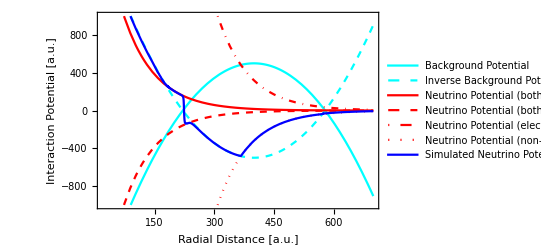

```mathematica
potNuTot[r_]:=potNu[scNu,stNu,r] (2 nu11[r]-1-as (2 anu11[r]-1))  (* simulated total neutrino potential *);

Plot[{potBG[xBG,yBG,wBG,r] (* background potential *),
-potBG[xBG,yBG,wBG,r] (* inverse of background potential *),
potNu[scNu,stNu,r]+potAnu[as,scNu,stNu,r] (* total neutrino potential with both electron type neutrino and antineutrino *),
-potNu[scNu,stNu,r]-potAnu[as,scNu,stNu,r]  (* total neutrino potential with both non-electron type neutrino and antineutrino *),
potNu[scNu,stNu,r]-potAnu[as,scNu,stNu,r] (* total neutrino potential with electron type neutrino and non-electron type antineutrino *), 
-potNu[scNu,stNu,r]+potAnu[as,scNu,stNu,r] (* total neutrino potential with non-electron type neutrino and electron type antineutrino *),
potNuTot[r] (* simulated total neutrino potential *)
},{r,rmin,rmax},PlotStyle->{Cyan,{Cyan,Dashed},Red,{Red,Dashed},{Red,DotDashed},{Red,Dotted},Blue},Frame->True, PlotRange->{{rmin,rmax},{-1000,1000}},Frame->True,
PlotStyle->{Cyan,{Cyan,Dashed},Red,{Red,Dashed},{Red,DotDashed},{Red,Dotted}},
FrameLabel->{"Radial Distance [a.u.]","Interaction Potential [a.u.]"},
FrameTicksStyle->Thick,
LabelStyle->Directive[FontSize->20],PlotLegends->{"Background Potential","Inverse Background Potential","Neutrino Potential (both electron type)","Neutrino Potential (both non-electron type)","Neutrino Potential (electron neutrino, non-electron antineutrino)","Neutrino Potential (non-electron neutrino, electron antineutrino)","Simulated Neutrino Potential"}
]
```

Fascinating!!! 
It turns out that the total neutrino potential follows the non-neutrino background potential due to actively maintained cancellation of the potentials. 
This is possible because both neutrinos and antineutrinos can change their types during the evolution. This phenomenon has been observed only very recently in the simulations of neutrino propagation in astrophysical environments (such as supernovae and neutron star/black hole mergers) and has been called as Matter-Neutrino-Resonance.
For more information, see: https://journals.aps.org/prd/abstract/10.1103/PhysRevD.94.093007 (and references therein).

Authorship information

Daavid Vaananen

June 19, 2017

djvaanan@ncsu.edu